```mathematica
eqn = (1-x)(1+y) == (1+x)(1-y)
```

```mathematica
(1-x) (1+y)==(1+x) (1-y)
```

(1-x) (1+y)==(1+x) (1-y)

```mathematica
Expand[eqn]
```

1-x+y-x y==1+x-y-x y

```mathematica
Collect[eqn, x]
```

1+y-x (1+y)==1+x (1-y)-y

```mathematica
Solve[a*x^2+b*x+c==0, x]
```

{{x→(-b-√(b^2-4 a c))/(2 a)},{x→(-b+√(b^2-4 a c))/(2 a)}}

```mathematica
Solve[
2x+3y==7 &&
3x+4y==10,
{x,y}
]
```

{{x→2,y→1}}

```mathematica
solution = Solve[
{
x^2 +y == 4,
2x-y ==1
},
{x,y}
]
```

{{x→-1-√6,y→-3-2 √6},{x→-1+√6,y→-3+2 √6}}

```mathematica
Sqrt[x^2+y^2]/.solution
```

```mathematica
{√((-3-2 √6)^2+(-1-√6)^2),√((-1+√6)^2+(-3+2 √6)^2)}
```

{√((-3-2 √6)^2+(-1-√6)^2),√((-1+√6)^2+(-3+2 √6)^2)}

```mathematica
Simplify[%]
```

{√(40+14 √6),√(40-14 √6)}

```mathematica
solution=Solve[-735+1337x-778x^2+198x^3-23x^4+x^5==0, x]
```

{{x→1},{x→3},{x→5},{x→7},{x→7}}

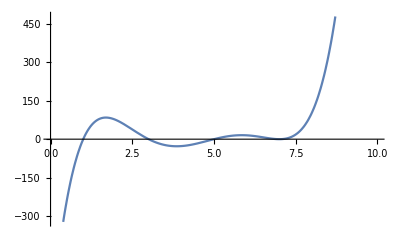

```mathematica
Plot[-735+1337x-778x^2+198x^3-23x^4+x^5, {x, 0, 10}]
```

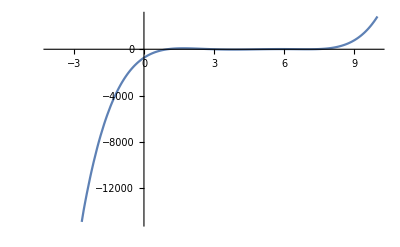

```mathematica
Plot[-735+1337x-778x^2+198x^3-23x^4+x^5, {x, -4, 10}]
```

```mathematica
NSolve[x^5==x+1, x]
```

{{x→-0.764884-0.352472 ⅈ},{x→-0.764884+0.352472 ⅈ},{x→0.181232-1.08395 ⅈ},{x→0.181232+1.08395 ⅈ},{x→1.1673}}

```mathematica
NSolve[x^5==x+1, x, 10]
```

{{x→-0.7648844336-0.352471546 ⅈ},{x→-0.7648844336+0.352471546 ⅈ},{x→0.181232444-1.083954101 ⅈ},{x→0.181232444+1.083954101 ⅈ},{x→1.167303978}}

```mathematica
Roots[x^3==x+1,x]
```

x==1/3 (27/2-(3 √69)/2)^(1/3)+(1/2 (9+√69))^(1/3)/3^(2/3)||x==-1/6 (1+ⅈ √3) (27/2-(3 √69)/2)^(1/3)-((1-ⅈ √3) (1/2 (9+√69))^(1/3))/(2 3^(2/3))||x==-1/6 (1-ⅈ √3) (27/2-(3 √69)/2)^(1/3)-((1+ⅈ √3) (1/2 (9+√69))^(1/3))/(2 3^(2/3))

```mathematica
NRoots[x^3==x+1,x]
```

x==-0.662359-0.56228 ⅈ||x==-0.662359+0.56228 ⅈ||x==1.32472

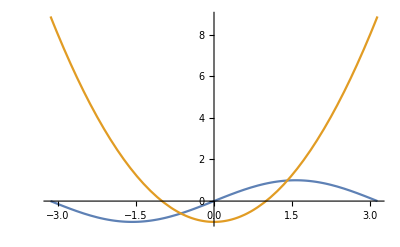

```mathematica
Plot[{Sin[x], x^2-1}, {x, -Pi, Pi}]
```

```mathematica
FindRoot[Sin[x] == x^2-1, {x, -1}]
```

{x→-0.636733}

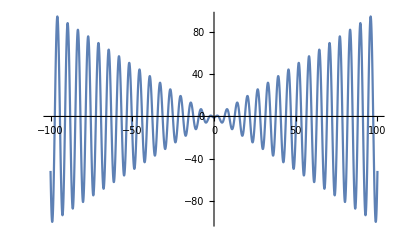

```mathematica
Plot[x*Sin[x]-1, {x, -100, 100}]
```

```mathematica
Plot[x*Sin[x]-1, {x, -10, 10}]
```

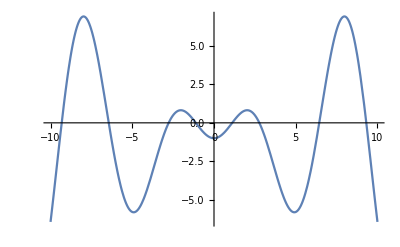

-Graphics-

```mathematica
a= {-9, -6, -3, -1, 1, 3, 6, 9}
```

{-9,-6,-3,-1,1,3,6,9}

```mathematica
Table[FindRoot[x*Sin[x]==1, {x, a[[i]]}], {i, 8}]
```

{{x→-9.31724},{x→-6.43912},{x→-2.7726},{x→-1.11416},{x→1.11416},{x→2.7726},{x→6.43912},{x→9.31724}}

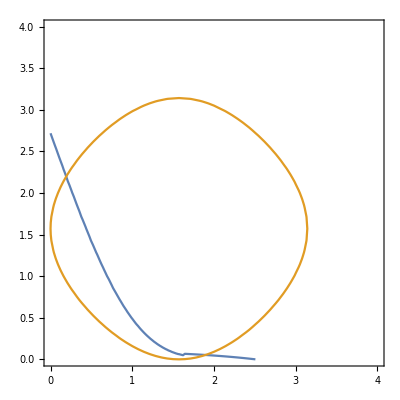

```mathematica
ContourPlot[{
Exp[x]+Log[y] == 2,
Sin[x]+Sin[y]==1},
{x, 0, 4},
{y,0,4}]
```

```mathematica
soll = FindRoot[{
Exp[x]+Log[y] == 2,
Sin[x]+Sin[y]==1},
{x, 0.4},
{y,2}]
```

{x→0.192202,y→2.19918}

```mathematica
soll = FindRoot[{
Exp[x]+Log[y] == 2,
Sin[x]+Sin[y]==1},
{x, 2},
{y,1}]
```

{x→1.77331-1.59497×10^-23 ⅈ,y→0.0204383-4.59574×10^-24 ⅈ}

```mathematica
Reduce[{3x-2y>a, x+y<b}, {x, y}]
```

b∈ℝ&&((x≤1/5 (9+2 b)&&y<1/2 (-9+3 x))||(x>1/5 (9+2 b)&&y<b-x))

```mathematica
FindInstance[{x^2+y^2==z^2, 0<x<y<z<=100}, {x,y,z}, Integers, 100]
```

{{x→3,y→4,z→5},{x→5,y→12,z→13},{x→6,y→8,z→10},{x→7,y→24,z→25},{x→8,y→15,z→17},{x→9,y→12,z→15},{x→9,y→40,z→41},{x→10,y→24,z→26},{x→11,y→60,z→61},{x→12,y→16,z→20},{x→12,y→35,z→37},{x→13,y→84,z→85},{x→14,y→48,z→50},{x→15,y→20,z→25},{x→15,y→36,z→39},{x→16,y→30,z→34},{x→16,y→63,z→65},{x→18,y→24,z→30},{x→18,y→80,z→82},{x→20,y→21,z→29},{x→20,y→48,z→52},{x→21,y→28,z→35},{x→21,y→72,z→75},{x→24,y→32,z→40},{x→24,y→45,z→51},{x→24,y→70,z→74},{x→25,y→60,z→65},{x→27,y→36,z→45},{x→28,y→45,z→53},{x→28,y→96,z→100},{x→30,y→40,z→50},{x→30,y→72,z→78},{x→32,y→60,z→68},{x→33,y→44,z→55},{x→33,y→56,z→65},{x→35,y→84,z→91},{x→36,y→48,z→60},{x→36,y→77,z→85},{x→39,y→52,z→65},{x→39,y→80,z→89},{x→40,y→42,z→58},{x→40,y→75,z→85},{x→42,y→56,z→70},{x→45,y→60,z→75},{x→48,y→55,z→73},{x→48,y→64,z→80},{x→51,y→68,z→85},{x→54,y→72,z→90},{x→57,y→76,z→95},{x→60,y→63,z→87},{x→60,y→80,z→100},{x→65,y→72,z→97}}

```mathematica
RecurrenceTable[
{s[n+2] == s[n+1]+s[n],
 s[1]==s[2] == 1},
s[n], {n, 1, 100}]
```

{1,1,2,3,5,8,13,21,34,55,89,144,233,377,610,987,1597,2584,4181,6765,10946,17711,28657,46368,75025,121393,196418,317811,514229,832040,1346269,2178309,3524578,5702887,9227465,14930352,24157817,39088169,63245986,102334155,165580141,267914296,433494437,701408733,1134903170,1836311903,2971215073,4807526976,7778742049,12586269025,20365011074,32951280099,53316291173,86267571272,139583862445,225851433717,365435296162,591286729879,956722026041,1548008755920,2504730781961,4052739537881,6557470319842,10610209857723,17167680177565,27777890035288,44945570212853,72723460248141,117669030460994,190392490709135,308061521170129,498454011879264,806515533049393,1304969544928657,2111485077978050,3416454622906707,5527939700884757,8944394323791464,14472334024676221,23416728348467685,37889062373143906,61305790721611591,99194853094755497,160500643816367088,259695496911122585,420196140727489673,679891637638612258,1100087778366101931,1779979416004714189,2880067194370816120,4660046610375530309,7540113804746346429,12200160415121876738,19740274219868223167,31940434634990099905,51680708854858323072,83621143489848422977,135301852344706746049,218922995834555169026,354224848179261915075}

```mathematica
RSolve[
b[1+n]==1/3 (x*b[n]+y), b[n], n]
```

{{b[n]→-(3^-n (3^n-x^n) y)/(-3+x)+3^(1-n) x^(-1+n) C[1]}}